# Finite Potential Well

## Even Solutions

```mathematica
m = 0.020;  (*mass of particle*)
U = 3*10^(-65); (*potential energy of surrounding box*)
En = 2*10^(-65); (*energy of particle*)
L = 1; (*length of box*)
h = 6.62607004*10^(-34); (*Planck;s constant*)
hbar = h/(2*Pi);   (* hbar = h/2pi*)

alpha = Sqrt[2*m*(U-En)]/hbar
beta = Sqrt[2*m*En]/hbar

Cl = Cos[beta*L/2]
Xl = Exp[-alpha*L/2]
E0 = (hbar^2)/(2*m)*(Pi/L)^2
ee = En/E0
uu = U/E0
```

5.99727

8.48143

-0.45438

0.049855

2.74405×10^-66

7.2885

10.9327

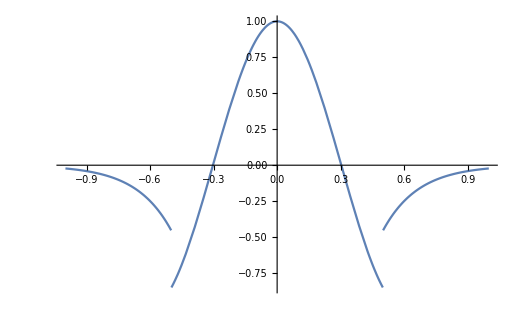

```mathematica
Plot[Piecewise[{{Cl/Xl*Exp[Pi*Sqrt[uu-ee]*x/L],x<-L/2},{Cos[Pi*Sqrt[E]*x/L],(x > -L/2) && (x < L/2)},{Cl/Xl*Exp[Pi*Sqrt[uu-ee]*(-x)/L],x>L/2}}],{x,-L,L}]
```

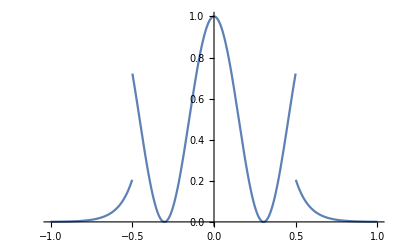

```mathematica
Plot[Piecewise[{{(Cl/Xl*Exp[Pi*Sqrt[uu-ee]*x/L])^2,x<-L/2},{(Cos[Pi*Sqrt[E]*x/L])^2,(x > -L/2) && (x < L/2)},{(Cl/Xl*Exp[Pi*Sqrt[uu-ee]*(-x)/L])^2,x>L/2}}],{x,-L,L}]
```

## Odd Solutions